Let’s do a 5x5 boxcar convolution on a 28x28 image. First straight-up for reference then in the MMB. H (height) increases more slowly than does W (width). Order indices from slowest to fastest.

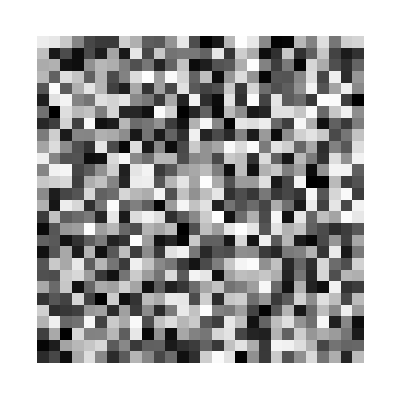

```mathematica
H=W=28;
(image=RandomReal[{0,1},{H,W}])//ArrayPlot
```

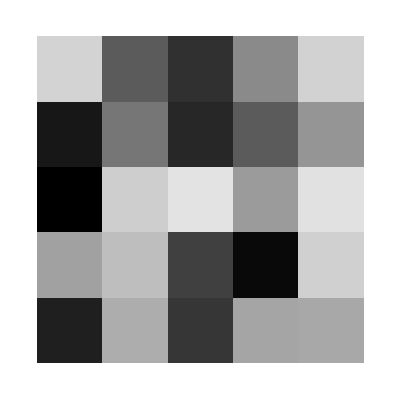

```mathematica
K=BOXW=BOXH=5;
(boxcar=RandomReal[{0,1},{K,K}])//(ArrayPlot[#,ImageSize->Tiny]&)
```

F1 on this symbol. Seems too general.

```mathematica
Convolve
```

Let’s do it by hand. The result will be 24x24. Write code with 0‑based indexing. Correct to 1‑based indexing only inside Mathematica’s double-bracket Part notation.

4

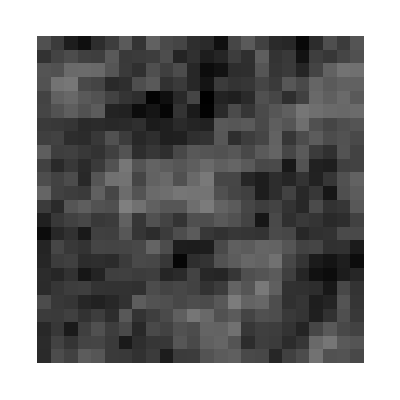

```mathematica
With[{d=Echo[2Floor[K/2]]},
Module[{output=ConstantArray[0,{H-d,W-d}],Hd=H-d,Wd=W-d,h,w,bh,bw},
For[h=0,h<Hd,h++,
For[w=0,w<Wd,w++,
For[bh=0,bh<K,bh++,
For[bw=0,bw<K,bw++,
output[[h+1,w+1]]+=image[[h+bh+1,w+bw+1]]*boxcar[[bh+1,bw+1]]]]]];
output
]]//ArrayPlot
```

Lay out the image and the boxcar in the MMB.

```mathematica
(halfbank=ConstantArray[0,{24,2048,16}]);
```

Relu 64 11 11, 32 26 26